## Front Matter

```mathematica
(* VERBOSE adds extra output *)
VERBOSE=True;
(* Assert adds extra checks *)
On[Assert];
Assert[FileExistsQ[NotebookDirectory[]<>"Libraries/q97_p389.wl"]]
Assert[FileExistsQ[NotebookDirectory[]<>"Libraries/polyiop.wl"]]
Assert[FileExistsQ[NotebookDirectory[]<>"Libraries/pairing_q97_p389"]]

Import[NotebookDirectory[]<>"Libraries/q97_p389.wl"]
Import[NotebookDirectory[]<>"Libraries/polyiop.wl"]
```

Elements of Gq: {25,236,65,69,169,335,206,93,380,164,210,193,157,35,97,91,330,81,80,55,208,143,74,294,348,142,49,58,283,73,269,112,77,369,278,337,256,176,121,302,159,85,180,221,79,30,361,78,5,125,13,325,345,67,119,252,76,344,42,272,187,7,175,96,66,94,16,11,275,262,326,370,303,184,321,245,290,248,365,178,171,385,289,223,129,113,102,216,343,17,36,122,327,6,150,249,1}

Roots of Unity: {1,22,96,75}

## Blah

0 | 1 | 0
0 | 1 | 1
1 | 1 | 1

{{{1,0},0},{{1,1},1},{{1,2},0},{{22,0},0},{{22,1},1},{{22,2},1},{{96,0},1},{{96,1},1},{{96,2},1}}

InterpolatingPolynomial::poised: The interpolation points {{1,0},{1,1},{1,2},{22,0},{22,1},{22,2},{96,0},{96,1},{96,2}} are not poised, so an interpolating polynomial of total degree 3 could not be found.

InterpolatingPolynomial[{{{1,0},0},{{1,1},1},{{1,2},0},{{22,0},0},{{22,1},1},{{22,2},1},{{96,0},1},{{96,1},1},{{96,2},1}},{X,Y}]

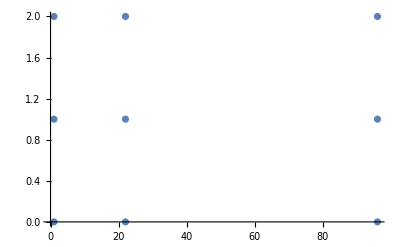

```mathematica
dd=3;

t=Table[{RandomInteger[1]},{i,1,dd},{j,1,dd}];
t//TableForm
Table[{{PowerMod[ω,i,q],j},First[t[[i+1,j+1]]]},{i,0,dd-1},{j,0,dd-1}];
points=Catenate[%]
InterpolatingPolynomial[points,{X,Y}]
ListPlot[First/@points]
```

1+65 x+31 x^2+18 y+67 x y+79 y^2

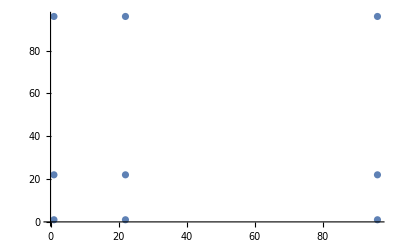

```mathematica
InterpolatingPolynomial[{{{0,0},1},{{1,0},0},{{0,1},1},{{2,1},1},{{3,3},0},{{1,2},1}},{x,y},Modulus->q];
Expand[%]
```

```mathematica
ω
MultiplicativeOrder[%,q]
```

22

4